Henry Osei

# Lab 7

## Experiment 7.1a

1) What is the maximum height achieved by a projectile thrown upward from height 6 and initial velocity 7

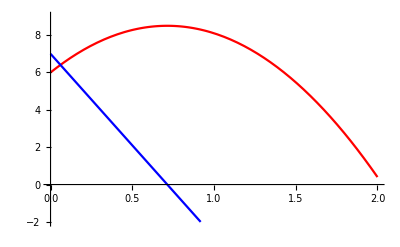

```mathematica
y[t_]:=6+7t-4.9t^2
Plot[{y[t],y'[t]},{t,0,1.5}, PlotRange->{-2,9},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
Solve[y'[t]==0,t]
```

{{t→0.714286}}

```mathematica
y[0.714286]
```

8.5

```mathematica
Maximum height is about 8.5
```

```mathematica
2) What is the maximum height achieved by a projectile thrown upward from height 8 and initial velocity 3?
```

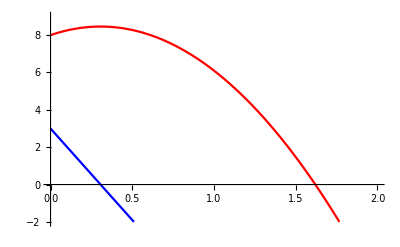

```mathematica
y[t_]:=8+3t-4.9t^2
Plot[{y[t],y'[t]},{t,0,2}, PlotRange->{-2,9},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
Solve[y'[t]==0,t]
```

```mathematica
{{t->0.3061224489795918}}
```

```mathematica
y[0.3061224489795918]
```

```mathematica
8.459183673469388
Maximum height is about 8.5
```

```mathematica
3) What is the maximum height achieved by a projectile thrown upward from height6and initial velocity16?
```

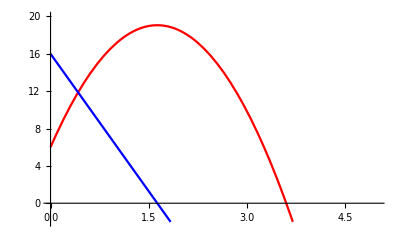

{{t→1.63265}}

```mathematica
y[t_]:=6+16t-4.9t^2
Plot[{y[t],y'[t]},{t,0,5}, PlotRange->{-2,20},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
Solve[y'[t]==0,t]
```

```mathematica
y[1.6326530612244896]
```

```mathematica
19.06122448979592
Maximum height is about 19.1


4) What is the maximum height achieved by a projectile thrown upward from height10and initial velocity12?
```

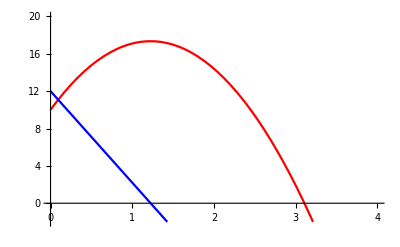

{{t→1.22449}}

```mathematica
y[t_]:=10+12t-4.9t^2
Plot[{y[t],y'[t]},{t,0,4}, PlotRange->{-2,20},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
Solve[y'[t]==0,t]
```

```mathematica
y[1.2244897959183672]
```

17.3469

```mathematica
Maximum height is about 17.3
```

## Experiment 7.1b

What is the maximum height achieved by a projectile thrown upward from height h and initial velocity v_0?

	Note that this problem can not be solved using graphical methods, but it can be solved with the aid of calculus.

```mathematica
y[t_]:=h+Subscript[v, 0]*t-g t^2/2
```

```mathematica
Solve [y'(t)==0, t]
y[Subscript[v, 0]/g]
```

{{t→0}}

h+v_0^2/(2 g)

## Experiment 7.1c

Using your results from Experiment 7.1b, verify your answers from Experiment 7.1a by replacing h and v_0 by their respective values.

```mathematica
1) What is the maximum height achieved by a projectile thrown upward from height 6 and initial velocity 7
```

```mathematica
6 + 7^2/(2*9.8)
```

8.5

```mathematica
2) What is the maximum height achieved by a projectile thrown upward from height 8 and initial velocity 3?
```

```mathematica
8 + 3^2/(2*9.8)
```

8.45918

```mathematica
3) What is the maximum height achieved by a projectile thrown upward from height6and initial velocity16?
```

```mathematica
6 + 16^2/(2*9.8)
```

19.0612

```mathematica
4) What is the maximum height achieved by a projectile thrown upward from height10and initial velocity12?
```

```mathematica
10 + 12^2/(2*9.8)
```

17.3469

## 7.2 Points where f'(x)=0.

Consider the function y(x)=sin(π x).

```mathematica
Clear[y,x];
y[x_]:=Sin[Pi x]
```

We can plot this function in red, and the derivative of this function in blue on the interval -2≤x≤2 with the command

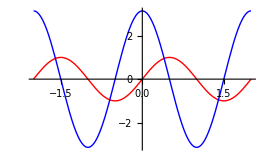

```mathematica
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

## Experiment 7.2

Finally, after answering these four questions for all functions below, draw a conclusion about the veracity of statements (1) and (2) .

	a) f(x)=x^2

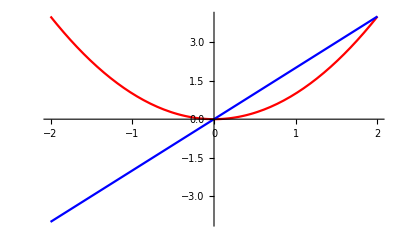

```mathematica
Clear[y,x];
y[x_]:=x^2
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
Function  has a relative   minimum  at x = 0
f'(x) = 0 at x = 0
Yes every relative maximum or relative minimum occur whenf' (x) = 0
Yes,every value ofxwheref' (x) = 0 is at a relative   maximum or relative  minimum 

b)f(x)=x^3
```

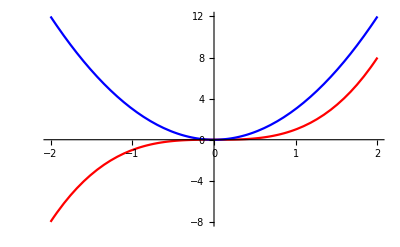

```mathematica
Clear[y,x];
y[x_]:=x^3
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
Function  has a relative  maximum  and  minimum   at x = 0
f'(x) = 0 at x = 0
Yes every relative maximum or relative minimum occur whenf' (x) = 0
Yes,every value ofxwheref' (x) = 0 is at a relative   maximum or relative  minimum
```

```mathematica
c)f(x)=x^4
```

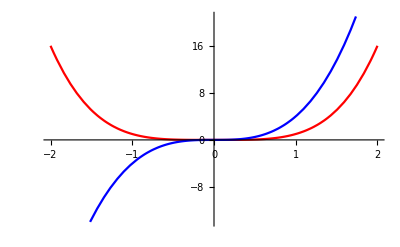

```mathematica
Clear[y,x];
y[x_]:=x^4
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
Function  has a relative  maximum  and  minimum   at x = 0
f'(x) = 0 at x = 0
Yes every relative maximum or relative minimum occur whenf' (x) = 0
Yes,every value ofxwheref' (x) = 0at a relative   maximum or relative  minimum
```

```mathematica
d)f(x)=x/(x^2+1)
```

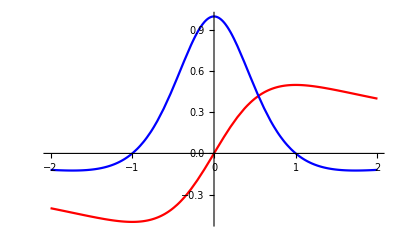

```mathematica
Clear[y,x];
y[x_]:=x/(x^2+1)
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
Function  has a relative  maximum  at x =1  and  a relative  minimum   at x = -1
f'(x) = 0 at x = 0
Yes every relative maximum or relative minimum occur whenf' (x) = 0
Yes,every value ofxwheref' (x) = 0 is at a relative   maximum or relative  minimum
```

```mathematica
e)f(x)=x sin (x/2)
```

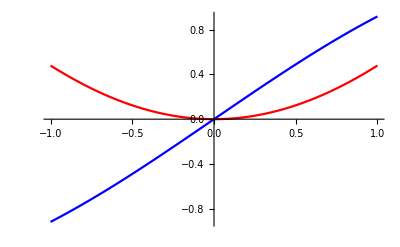

```mathematica
Clear[y,x];
y[x_]:=x*Sin[x/2]
Plot[{y[x],y'[x]},{x,-1,1},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
Function  has a relative   minimum  at x = 0
f'(x) = 0 at x = 0
Yes every relative maximum or relative minimum occur whenf' (x) = 0
Yes,every value ofxwheref' (x) = 0 is at a relative   maximum or relative  minimum
```

```mathematica
f) f(x)=x^2 sin x
```

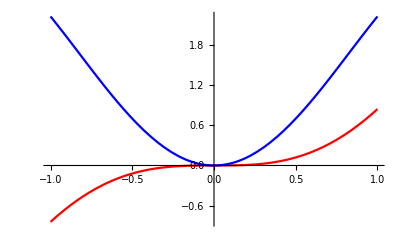

```mathematica
Clear[y,x];
y[x_]:=x^2Sin[x]
Plot[{y[x],y'[x]},{x,-1,1},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
Function  has a relative  maximum and   minimum  at x = 0
f'(x) = 0 at x = 0
Yes every relative maximum or relative minimum occur whenf' (x) = 0
Yes,every value ofxwheref' (x) = 0 is at a relative   maximum or relative  minimum
```

## 7.3 Critical Points

```mathematica
Ab[x_]:=Sqrt[x^2]
```

Now we can define our function y(x)=|sin x| as follows.

```mathematica
Clear[y,x];
y[x_]:= Ab[Sin[x]];
```

We can then plot this function and its derivative just as we did before, with the command

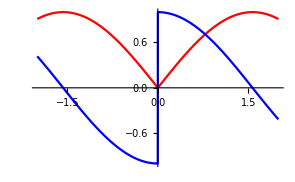

```mathematica
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

(1*) For any function y=f(x), if f has a relative maximum or a relative minimum at the point z, then z is a critical point for f .
	(2*) For any function y=f(x), if f has a critical point at z, then f has a relative maximum or relative minimum at the point z.

We would like to know which, if either of these statements are true.

## Experiment 7.3

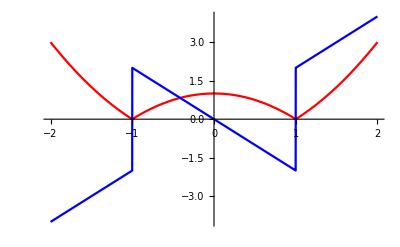

```mathematica
Clear[y,x];
y[x_]:= Ab[x^2-1];
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
f(x) is a relative   minimum at x = -1 and x = 1. It is a relatve maximum at x =0
f(x) has critical points at x= 0 
No. The minimums  at x =-1 and x=1 do not occur at critical points  because f'(x) ≠ 0 at those  x values
Yes.
```

```mathematica
b) f(x)=|1/2-sin x|
```

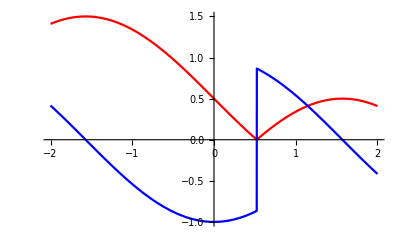

```mathematica
Clear[y,x];
y[x_]:= Ab[0.5-Sin[x]];
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
f(x) is a relative   maximum  at x = -1.6  and x = 1.6. It is a relatve  minimum at x =0.5
f(x) has critical points at x= -1.6 and 1.6
No. The minimum  at x =0.5 do not occur at critical points  because f'(x) ≠ 0 at that  x value
Yes.
```

```mathematica
c) f(x)=|x|^(2/ 3)
```

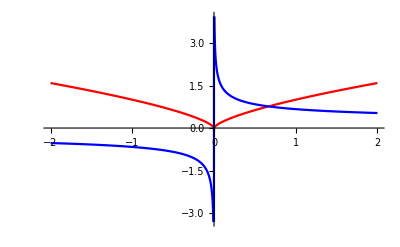

```mathematica
Clear[y,x];
y[x_]:= Ab[x]^(2/3);
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
f(x) is a relative   minimum at x = 0
f(x) has no critical points 
No. f has a relative minimum but no critical point
Not applicable
```

```mathematica
In conclusion, every  critical    point    is    a   relative    minimum    or    maximum   but    not    every    minimum or maximum occurs at a critical point
```

## 7.4 The First Derivative Test

As an example, consider the function f(x)=4 x^2-2 x^4

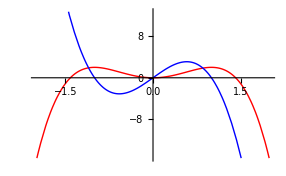

```mathematica
Clear[x,y];
y[x_]=4x^2-2x^4;
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

## Experiment 7.4

For each of the following functions, plot the function and its derivative on the same graph. 

	a) f(x)=sin((x^2-1)/(x^2+2))			b) f(x)=e^(-x^2/2)		c) f(x)=exp(x/(x^2+2))
	
	d) f(x)=3sin((2 x^3)/(x^4+1))		e) f(x)=(-2 x^3)/(x^2+2)

Sin[(-1+x^2)/(2+x^2)]

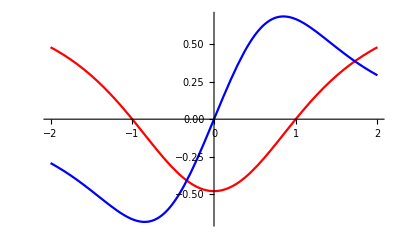

```mathematica
Clear[x,y];
y[x_]=Sin[(x^2-1)/(x^2+2)]
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
(a) For x near c we have f'(x)<0 when x<c and f'(x)>0 when x>c.
```

```mathematica
b) f(x)=e^(-x^2/2)
```

ⅇ^(-x^2/2)

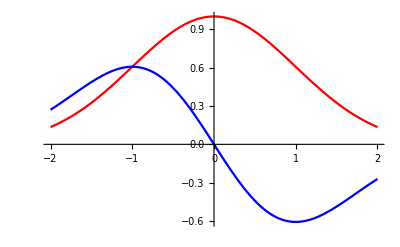

```mathematica
Clear[x,y];
y[x_]=Exp[-x^2/2]
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
(b) For x near c we have f'(x)>0 when x<c and f'(x)<0 when x>c.
```

```mathematica
e) f(x)=(-2 x^3)/(x^2+2)
```

-(2 x^3)/(2+x^2)

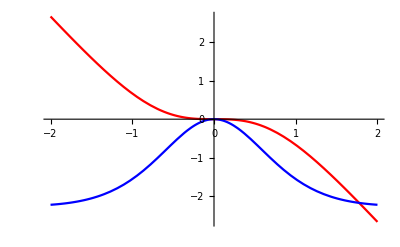

```mathematica
Clear[x,y];
y[x_]=-2x^3/(x^2 +2)
Plot[{y[x],y'[x]},{x,-2,2},PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,0,1]}}]
```

```mathematica
(c) For x near c we have f'(x)<0 when x<c and f'(x)<0 when x>c.
```